1. Which is useful for defining piecewise functions.

```mathematica
aPiecewiseFunction[x_?NumberQ]:=Which[x≤-1,Sqrt[-x-1],x≥1,Sqrt[x-1],True,1-x^2]
```

Now we plot it.

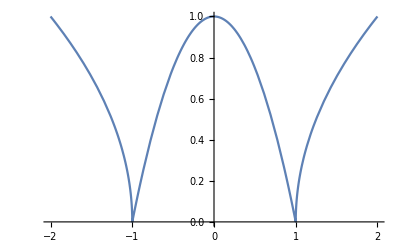

```mathematica
Plot[aPiecewiseFunction[x],{x,-2,2}]
```